# AntonAntonov/VariableImportanceByClassifiers

Variables importance determination using classifiers

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"AccuracyByVariableShuffling.nb"DocumentationEnglishReferencePagesSymbolsAccuracyByVariableShuffling.nb

"Tutorials"

"Importanceofvariablesinvestigation.nb"DocumentationEnglishTutorialsImportanceofvariablesinvestigation.nb

"Kernel"

"VariableImportanceByClassifiers.wl"KernelVariableImportanceByClassifiers.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This paclet has functions for finding the importance of variables in datasets using classifiers.

### Details

Any classifier made with Classify can be used within the paclet.

Ensemble classifiers made with functions of the paclet "ClassifierEnsembles" can be also used.

Importance is assessed by shuffling the values of each variable's column in the test data.

The most significant drop in performance after shuffling indicates the most important or decisive variables.

### Primary Context

AntonAntonov`VariableImportanceByClassifiers`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`VariableImportanceByClassifiers`"];
```

### Basic Examples

1. Load some data:

```mathematica
testSetName = "Titanic"; (* "Mushroom" "Titanic" *)
 trainingSet = ExampleData[{"MachineLearning", testSetName}, "TrainingData"];
 testSet = ExampleData[{"MachineLearning", testSetName}, "TestData"];
```

2. Variable names and unique class labels.:

```mathematica
varNames = Flatten[List @@ ExampleData[{"MachineLearning", testSetName}, "VariableDescriptions"]]
```

{passenger class,passenger age,passenger sex,passenger survival}

```mathematica
classLabels = Union[ExampleData[{"MachineLearning", testSetName}, "Data"][[All, -1]]]
```

{died,survived}

3. Here is a data summary:

```mathematica
Grid[List@ResourceFunction["RecordsSummary"][(Flatten/@(List@@@Join[trainingSet,testSet]))/._Missing->0,varNames],Dividers->All,Alignment->{Left,Top}]
```

1 passenger class
3rd | 709
1st | 323
2nd | 277 | 2 passenger age
Min | 0
1st Qu | 7.
Mean | 23.8775
Median | 24.
3rd Qu | 35.
Max | 80. | 3 passenger sex
male | 843
female | 466 | 4 passenger survival
died | 809
survived | 500

4. Make the classifier:

```mathematica
clFunc = Classify[trainingSet, Method -> "RandomForest"]
```

ClassifierFunction[…]

5. Obtain accuracies after shuffling:

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames]
```

<|None→0.778626,passenger class→0.694656,passenger age→0.778626,passenger sex→0.618321|>

6. Tabulate the results:

```mathematica
ResourceFunction["GridTableForm"][List @@@ Normal[accs/First[accs]],TableHeadings->{"shuffled variable", "accuracy ratio"}]
```

# | shuffled variable | accuracy ratio
1 | None | 1.
2 | passenger class | 0.892157
3 | passenger age | 1.
4 | passenger sex | 0.794118

7. Further confirmation of the found variable importance can be done using the mosaic plots.
 We can see that female passengers are much more likely to survive and especially female passengers from first and second class:

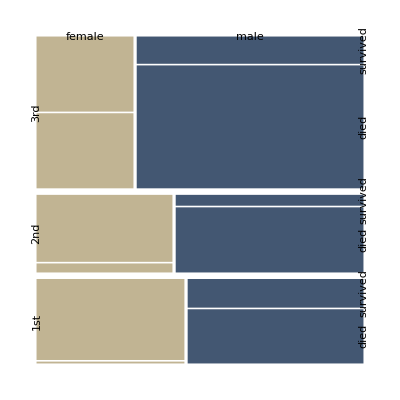

```mathematica
t = DeleteCases[(Flatten /@ (List @@@ trainingSet)),{___,_Missing,___}];
 {{-Graphics-, MosaicPlot}}[t[[All, {1,3,4}]], ColorRules -> {2-> ColorData[7, "ColorList"]} ,"LabelRotation"->{{1,0.45},{0,1}}]
```

5a. In order to use F-scores instead of overall accuracy the desired class labels are specified with
 the option "ClassLabels":

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames, "ClassLabels" -> classLabels]
```

<|None→{0.74375,0.931507},passenger class→{0.678899,0.681818},passenger age→{0.745283,0.92},passenger sex→{0.661677,0.627119}|>

5b. Here is another example that uses the class label with the smallest F-score.
 (Probably the most important since it is most misclassified):

```mathematica
accs = AccuracyByVariableShuffling[clFunc, testSet, varNames,"ClassLabels" -> Position[#, Min[#]][[1, 1, 1]] &@ClassifierMeasurements[clFunc, testSet, "FScore"]]
```

<|None→{0.931507},passenger class→{0.714286},passenger age→{0.918919},passenger sex→{0.576271}|>

5c. It is good idea to verify that we get the same results using different classifiers. Below is given code that computes the shuffled accuracies and returns the relative damage scores for a set of methods of Classify:

```mathematica
mres=Association@Map[
Function[{clMethod},
cf=Classify[trainingSet,Method->clMethod];
accRes=AccuracyByVariableShuffling[cf,testSet,varNames,"ClassLabels"->"survived"];
clMethod->(accRes[None]-Rest[accRes])/accRes[None]
],{"LogisticRegression","NearestNeighbors","GradientBoostedTrees","RandomForest","SupportVectorMachine"}] ;
Dataset[mres]
```

-Graphics-

### Scope

#### Using classifier ensembles

Make a classifier ensemble:

```mathematica
aCLs={{-Graphics-, EnsembleClassifier}}[{"LogisticRegression","NearestNeighbors","RandomForest"},trainingSet];
aCLs//Rasterize
```

-Graphics-

Obtain accuracies after shuffling:

```mathematica
accs = AccuracyByVariableShuffling[aCLs, testSet, varNames]
```

<|None→0.78626,passenger class→0.720102,passenger age→0.783715,passenger sex→0.59542|>

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-VariableImportanceByClassifiers-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Classifier

Variable importance

Machine Learning

Classification

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/ClassifierEnsembles

AntonAntonov/MosaicPlot

### Original Source References and Attributions

Importance of variables investigation | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/VariableImportanceByClassifiers.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

12.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.